# Sinc scalar error for the approximations

Error bound for the scalar approximation based on the Padé formula for the ϕ functions.

```mathematica
sinc[z_]:= Sin[z]/z;
ES[n_,z_] := (- 1)/(2 ⅈ z) (LaguerreL[n,-2n-1,-ⅈ z]^2-LaguerreL[n,-2n-1,ⅈ z]^2)/(LaguerreL[n,-2n-1,ⅈ z]LaguerreL[n,-2n-1,-ⅈ z]);
SN[n_,x_] :=  Factorial[n]^2/(Factorial[2n] Factorial[2n+1])z^(2n);
{{ERR[n_,z_]:= Abs[sinc[z]-ES[n,z]];}, {□}}
BoundE[n_,z_]:= ((2^(n+1)Factorial[n])/Factorial[2n+1])^2 z^(2n+1);
Bound2E[n_,z_]:= SN[n,z];
```

{{Null},{□}}

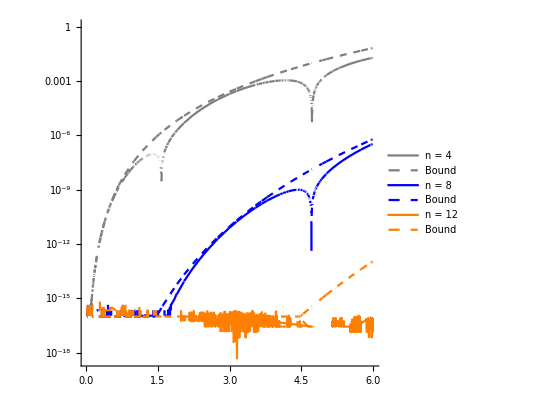

```mathematica
bound1 = Plot[{ERR[4,z],Max[10^-16,Abs[Bound2E[4,z]]],ERR[8,z],Max[10^-16,Abs[Bound2E[8,z]]],ERR[16,z],Max[10^-16,Abs[Bound2E[12,z]]]},{z,0.01,6},ScalingFunctions->"Log",PlotLegends->{"n = 4","Bound","n = 8","Bound","n = 12","Bound"},PlotStyle->{Gray,{Gray, Dashed},Blue,{Blue, Dashed},Orange,{Orange, Dashed}},AspectRatio->1,TicksStyle->Large]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["boundexp.eps",bound1];
```

Error bound for the case in which we use the Padé approximation based on the Hypergeometric function.

```mathematica
c[n_,x_]:= (-x)^n Gamma[n+2]/Gamma[2n+2];
phat[n_,x_]:= Sum[(Pochhammer[-n,k]Pochhammer[n+2,k])/(Pochhammer[2,k]Factorial[k])HypergeometricPFQ[{-n+k,n+2+k,1},{1+k},1/x],{k,0,n}];
p[n_,x_]:= c[n,x]phat[n,x];
FN[n_,z_]:= (-1)^n Binomial[2n+1,n] p[n,-2ⅈ z]/LaguerreL[n,-2n-2,2 ⅈ z] Exp[ⅈ z];
ERR2[n_,z_]:= Abs[sinc[z]-FN[n,z]];
```

```mathematica
RN[n_,x_]:= ((-1)^(n+1)π x^(2n+1)Exp[ (-x+x(x+4))/(4(2n+2))])/(2^(4n+3)Gamma[n+3/2]^2)
RNhat[n_,z_] := RN[n,2ⅈ z]Exp[ⅈ z];
```

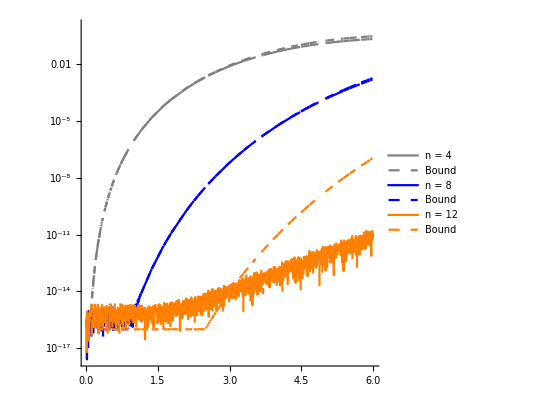

```mathematica
bound2 = Plot[{ERR2[4,z],Max[10^-16,Abs[RNhat[4,z]]],ERR2[8,z],Max[10^-16,Abs[RNhat[8,z]]],ERR2[16,z],Max[10^-16,Abs[RNhat[12,z]]]},{z,0.01,6},ScalingFunctions->"Log",PlotLegends->{"n = 4","Bound","n = 8","Bound","n = 12","Bound"},PlotStyle->{Gray,{Gray, Dashed},Blue,{Blue, Dashed},Orange,{Orange, Dashed}},AspectRatio->1,TicksStyle->Large]
```

```mathematica
Export["boundf11.eps",bound2];
```

```mathematica
(* Error Bound with symmetrized approximation *)
```

```mathematica
A [n_,x_]:=Gamma[n+2]/Gamma[2n+2] x^n Sum[(Pochhammer[-n,k]Pochhammer[n+2,k])/(Pochhammer[2,k]Factorial[k])HypergeometricPFQ[{-n+k,n+2+k,1},{1+k},-1/x],{k,0,n}];
FN[n_,z_]:= (-1)^n/2 Binomial[2n+1,n](A[n,ⅈ z]LaguerreL[n,-2n-2,-ⅈ z]+A[n,-ⅈ z]LaguerreL[n,-2n-2,ⅈ z])/(LaguerreL[n,-2n-2,ⅈ z]LaguerreL[n,-2n-2,-ⅈ z]);
ERR3[n_,z_]:= N[Abs[sinc[z]-FN[n,z]]];
```

```mathematica
RNtilda[n_,x_]:= -Factorial[n+1]^2/(Factorial[2n+1]Factorial[2n+3])x^(2n+2);
```

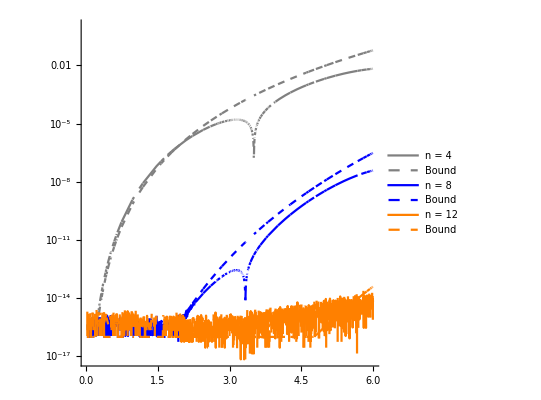

```mathematica
bound3 = Plot[{ERR3[4,z],Max[10^-16,Abs[RNtilda[4,z]]],ERR3[8,z],Max[10^-16,Abs[RNtilda[8,z]]],ERR3[16,z],Max[10^-16,Abs[RNtilda[12,z]]]},{z,0.01,6},ScalingFunctions->"Log",PlotLegends->{"n = 4","Bound","n = 8","Bound","n = 12","Bound"},PlotStyle->{Gray,{Gray, Dashed},Blue,{Blue, Dashed},Orange,{Orange, Dashed}},AspectRatio->1,TicksStyle->Large]
```

```mathematica
Export["boundf11-2.eps",bound3];
```